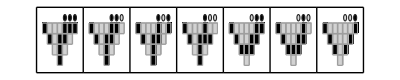
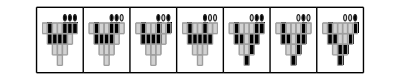
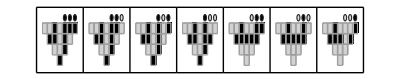
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Labeled[GraphicsRow[Table[Show[{ArrayPlot[MapIndexed[If[Abs[4-#2[[2]]]<5-#2[[1]],#1-.15,0]&,CellularAutomaton[30,Join[#,IntegerDigits[n,2,3]],3],{2}],],Graphics[{EdgeForm[GrayLevel[.15]],MapIndexed[{GrayLevel[.85-#1],Disk[{3+First[#2],4}+.5,.3]}&,IntegerDigits[n,2,3]]}]}],{n,7,1,-1}],],ArrayPlot[{Join[#,{1,1,1}]},],Left]&/@{{1,0,0,0},{0,1,0,0},{0,0,1,0}}
```